## Week 7 - Lecture 8: Estimating π using Buffon's Needle Drop Problem

Resources  --  Video  &  Notes 7h

Straightforward estimation of π using Monte-Carlo. Check pages 2-3.
Let us first compute x^2+y^2 by generating {x,y} (2 numbers) randomly. 
Note that we consider the first quadrant only since that's sufficient.

```mathematica
RandomReal[{0,1}, 2]^2 (*When summed gives r^2, which is 1 for unit circle inside unit square*)
```

{0.0761129,0.0317726}

To check if a given random x,y is on the circle region:

```mathematica
If[
(RandomReal[{0,1}, 2]^2 // Total) ≤ 1, (*Condition*)
1, (*Return value for true case*)
0] (*Return value for false case*)
```

1

Let us now write the Monte Carlo. Essentially, π = 4*(circle_area/square_area)

```mathematica
nMax=1000000;
dataset = Table[
ratio=Mean[Table[If[(RandomReal[{0,1}, 2]^2 // Total) ≤ 1,1,0], {nMax}]];
4.0*ratio, {100}]; // Timing
```

{46.835,Null}

3.14174

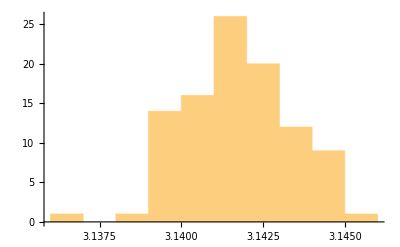

```mathematica
Mean[dataset]
Histogram[dataset]
```

Homework:
- Try playing with nMax and compare Timings
- Try calculating error bars for different nMax and averaging_trials
- Compare this method's timing/accuracy to the MC based on importance sampling and the naive one.